```mathematica
ClearAll["Global`*"]
```

### Data

```mathematica
max=5;
dx= 0.1;
xpts=241;
ypts=241;

t0=0.25;
tf=7.25;
dt=1.;

xmin=-dx*(xpts-1)/2;
xmax=dx*(xpts-1)/2;
s1=1 + xpts * (ypts-1)/2 ;
s2=s1+xpts-1;

wd=SetDirectory@NotebookDirectory[];
anisoPath=wd<>"/../../output";
viscousPath=wd<>"/output";

t0str =NumberForm[t0,{3,3}]//ToString;
t1str=NumberForm[t0+1*dt,{3,3}]//ToString;
t2str=NumberForm[t0+2*dt,{3,3}]//ToString;
t3str=NumberForm[t0+3*dt,{3,3}]//ToString;
t4str=NumberForm[t0+4*dt,{3,3}]//ToString;
t5str=NumberForm[t0+5*dt,{3,3}]//ToString;
t6str=NumberForm[t0+6*dt,{3,3}]//ToString;
t7str=NumberForm[t0+7*dt,{3,3}]//ToString;

Ratio1=Table[{xmin+i*dx,1.0},{i,0,xpts-1}];
```

```mathematica
(* aniso hydro *)

e0aniso=Take[Import[anisoPath<>"/e_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
e1aniso=Take[Import[anisoPath<>"/e_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
e2aniso=Take[Import[anisoPath<>"/e_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
e3aniso=Take[Import[anisoPath<>"/e_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
e4aniso=Take[Import[anisoPath<>"/e_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
e5aniso=Take[Import[anisoPath<>"/e_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
e6aniso=Take[Import[anisoPath<>"/e_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
e7aniso=Take[Import[anisoPath<>"/e_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];

plpt0aniso=Take[Import[anisoPath<>"/plpt_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
plpt1aniso=Take[Import[anisoPath<>"/plpt_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
plpt2aniso=Take[Import[anisoPath<>"/plpt_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
plpt3aniso=Take[Import[anisoPath<>"/plpt_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
plpt4aniso=Take[Import[anisoPath<>"/plpt_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
plpt5aniso=Take[Import[anisoPath<>"/plpt_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
plpt6aniso=Take[Import[anisoPath<>"/plpt_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
plpt7aniso=Take[Import[anisoPath<>"/plpt_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];

pi0aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
pi1aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
pi2aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
pi3aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
pi4aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
pi5aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
pi6aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
pi7aniso=Take[Import[anisoPath<>"/RpiT_inv_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];

ux0aniso=Take[Import[anisoPath<>"/ux_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
ux1aniso=Take[Import[anisoPath<>"/ux_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
ux2aniso=Take[Import[anisoPath<>"/ux_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
ux3aniso=Take[Import[anisoPath<>"/ux_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
ux4aniso=Take[Import[anisoPath<>"/ux_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
ux5aniso=Take[Import[anisoPath<>"/ux_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
ux6aniso=Take[Import[anisoPath<>"/ux_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
ux7aniso=Take[Import[anisoPath<>"/ux_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];
```

```mathematica
(* viscous hydro *)
e0viscous=Take[Import[viscousPath<>"/e_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
e1viscous=Take[Import[viscousPath<>"/e_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
e2viscous=Take[Import[viscousPath<>"/e_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
e3viscous=Take[Import[viscousPath<>"/e_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
e4viscous=Take[Import[viscousPath<>"/e_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
e5viscous=Take[Import[viscousPath<>"/e_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
e6viscous=Take[Import[viscousPath<>"/e_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
e7viscous=Take[Import[viscousPath<>"/e_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];

plpt0viscous=Take[Import[viscousPath<>"/plpt_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
plpt1viscous=Take[Import[viscousPath<>"/plpt_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
plpt2viscous=Take[Import[viscousPath<>"/plpt_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
plpt3viscous=Take[Import[viscousPath<>"/plpt_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
plpt4viscous=Take[Import[viscousPath<>"/plpt_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
plpt5viscous=Take[Import[viscousPath<>"/plpt_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
plpt6viscous=Take[Import[viscousPath<>"/plpt_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
plpt7viscous=Take[Import[viscousPath<>"/plpt_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];

pi0viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
pi1viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
pi2viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
pi3viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
pi4viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
pi5viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
pi6viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
pi7viscous=Take[Import[viscousPath<>"/RpiT_inv_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];

ux0viscous=Take[Import[viscousPath<>"/ux_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
ux1viscous=Take[Import[viscousPath<>"/ux_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
ux2viscous=Take[Import[viscousPath<>"/ux_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
ux3viscous=Take[Import[viscousPath<>"/ux_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
ux4viscous=Take[Import[viscousPath<>"/ux_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
ux5viscous=Take[Import[viscousPath<>"/ux_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
ux6viscous=Take[Import[viscousPath<>"/ux_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];
ux7viscous=Take[Import[viscousPath<>"/ux_"<>t7str<>".dat"]][[s1;;s2,{1,4}]];
```

### Colors and Labels

```mathematica
colors={Darker[Blue],Blue,Cyan, Green,Yellow,Orange ,Red,Darker[Red]};
colorpts=Table[1.0*i/(Length[colors]-1),{i,0,Length[colors]-1}];

Unprotect[ColorData];
ColorData["Energy"]=Function[x,Blend[Transpose[{colorpts,colors}],x ]];
ColorData["Flow"]=Function[x,Blend[Transpose[{colorpts,colors}],x / max]];
Protect[ColorData];

Grid[{{BarLegend[{ColorData["Energy"],{0,1}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],
BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]}}];

magentaTran={Blend[{Red,Magenta},0.5],AbsoluteThickness[1.5],Opacity[0.3]};
redTran={Red,AbsoluteThickness[1.5],Opacity[0.3]};
orangeTran={Blend[{Red,Orange},0.75],AbsoluteThickness[1.5],Opacity[0.3]};
yellowTran={Blend[{Orange,Yellow},0.5],AbsoluteThickness[1.5],Opacity[0.3]};
greenTran={Blend[{Blue,Green},0.875],AbsoluteThickness[1.5],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[1.5],Opacity[0.3]};
cyanTran={Blend[{Blue,Cyan},0.75],AbsoluteThickness[1.5],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[1.5],Opacity[0.3]};
purpleTran={Blend[{Blue,Purple},0.75],AbsoluteThickness[1.5],Opacity[0.3]};

magenta={Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
red={Red,AbsoluteDashing[{8,6.5}],AbsoluteThickness[1.5]};
yellow={Blend[{Orange,Yellow},0.5],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
orange={Blend[{Red,Orange},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
green={Blend[{Blue,Green},0.875],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
cyan={Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
blue={Blue,AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
purple={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};

magentaSolid={Blend[{Red,Magenta},0.5],AbsoluteThickness[1.5]};
redSolid={Red,AbsoluteThickness[1.5]};
yellowSolid={Blend[{Orange,Yellow},0.5],AbsoluteThickness[1.5]};
orangeSolid={Blend[{Red,Orange},0.75],AbsoluteThickness[1.5]};
greenSolid={Blend[{Blue,Green},0.875],AbsoluteThickness[1.5]};
cyanSolid={Blend[{Blue,Cyan},0.75],AbsoluteThickness[1.5]};
blueSolid={Blue,AbsoluteThickness[1.5]};
purpleSolid={Blend[{Blue,Purple},0.75],AbsoluteThickness[1.5]};
blackSolid={Black,AbsoluteThickness[1.5]};

style={magentaTran,redTran,orangeTran,yellowTran,greenTran,cyanTran,blueTran,purpleTran,magenta,red,orange,yellow,green,cyan, blue,purple};
styleSolid={magentaSolid,redSolid,orangeSolid,greenSolid,cyanSolid, blueSolid,purpleSolid};


(* Plot Labels *)
eLabel=Panel[Grid[{{Style["ℰ",FontSize->20,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
uxLabel=Panel[Grid[{{Style["u_x",FontSize->20,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
plptLabel=Panel[Grid[{{Style["(P_(L_((<>)_(<>))))/(P_⊥)",FontSize->24,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
piLabel=Panel[Grid[{{Style["(√(π_(⊥_(<>))))/(P_⊥)",FontSize->24,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
size=25;

legendTimes3=Grid[{{Graphics[{Directive[Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 0.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Red,AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 1.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Red,Orange},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 2.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Orange,Yellow},0.5],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 3.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Green},0.875],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 4.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 5.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blue,AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 6.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 7.01 fm/c",FontSize->12.75,FontFamily->"Arial"]}
}];

legend1=Panel[Grid[{{Graphics[{Directive[RGBColor[1,0,0.1],AbsoluteDashing[{8,6}],AbsoluteThickness[2.5]],Line[{{0,0},{1,0}}]},ImageSize->38,AspectRatio->0.5],Style["CPU VAH",FontSize->14,FontFamily->"Arial"]},
{Graphics[{Directive[Red,Opacity[0.3],AbsoluteThickness[2.5]],Line[{{0,0},{1,0}}]},ImageSize->38,AspectRatio->0.5],Style["CPU VH",FontSize->14,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

initTime1=Style["  τ_0 = 0.01 fm/c",FontSize->13,FontFamily->"Arial"];

initEta=Style["η_(<>)/_(<>)s = 0.08",FontSize->13,FontFamily->"Arial"];

spaceresLabel1=Grid[{
{Style["Δx = 0.1 fm",FontSize->13,FontFamily->"Arial"]},
{Style["Δy = 0.1 fm",FontSize->13,FontFamily->"Arial"]}}];

gridLabel1=Style["Grid: 24 fm × 24 fm",FontSize->13,FontFamily->"Arial"];

plptLabel1=Style["P_L0/P_(⊥0) = 10^-3",FontSize->13,FontFamily->"Arial"];

TLabel1=Style["T_0 = 1.35 GeV",FontSize->13,FontFamily->"Arial"];
```

### Ticks

```mathematica
min = {0.009,0};
maj={0.016,0};

logticks = {{0.0001,"10^-4",maj},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"10^-3",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"0.01",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},
{0.1,"0.1",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},
{1,"1",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},
{10,"10",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",min},{60,"",min},{70,"",min},{80,"",min},{90,"",min},
{100,"100",maj},{200,"",min},{300,"",min},{400,"",min},{500,"",min},{600,"",min},{700,"",min},{800,"",min},{900,"",min},
{1000,"10^3",maj},{2000,"",min},{3000,"",min},{4000,"",min},{5000,"",min},{6000,"",min},{7000,"",min},{8000,"",min},{9000,"",min},{10000,"10^4",maj},{20000,"",min}};

nologticks =  {{0.0001,"",maj},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},
{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},
{1,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},
{10,"",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",min},{60,"",min},{70,"",min},{80,"",min},{90,"",min},
{100,"",maj},{200,"",min},{300,"",min},{400,"",min},{500,"",min},{600,"",min},{700,"",min},{800,"",min},{900,"",min},
{1000,"",maj},{2000,"",min},{3000,"",min},{4000,"",min},{5000,"",min},{6000,"",min},{7000,"",min},{8000,"",min},{9000,"",min},{10000,"",maj},{20000,"",min}};

xticks ={{-12,"",min},{-11,"",min},
{-10,"-10",maj},{-9,"",min},{-8,"",min},{-7,"",min},{-6,"",min},
{-5,"-5",maj},{-4,"",min},{-3,"",min},{-2,"",min},{-1,"",min},
{0,"0",maj},
{1,"",min},{2,"",min},{3,"",min},{4,"",min},{5,"5",maj},
{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"10",maj},
{11,"",maj},{12,"",min}};

noxticks ={{-12,"",min},{-11,"",min},
{-10,"",maj},{-9,"",min},{-8,"",min},{-7,"",min},{-6,"",min},
{-5,"",maj},{-4,"",min},{-3,"",min},{-2,"",min},{-1,"",min},
{0,"",maj},
{1,"",min},{2,"",min},{3,"",min},{4,"",min},{5,"",maj},
{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"",maj},
{11,"",maj},{12,"",min}};

uxticks ={{-5,"-5",maj},{-4.75,"",min},{-4.5,"",min},{-4.25,"",min},{-4,"-4",maj},
{-3.75,"",min},{-3.5,"",min},{-3.25,"",min},{-3,"-3",maj},
{-2.75,"",min},{-2.5,"",min},{-2.25,"",min},{-2,"-2",maj},
{-1.75,"",min},{-1.5,"",min},{-1.25,"",min},{-1,"-1",maj},
{-0.75,"",min},{-0.5,"",min},{-0.25,"",min},
{0,"0",maj},
{0.25,"",min},{0.5,"",min},{0.75,"",min},{1,"1",maj},
{1.25,"",min},{1.5,"",min},{1.75,"",min},{2,"2",maj},
{2.25,"",min},{2.5,"",min},{2.75,"",min},{3,"3",maj},
{3.25,"",min},{3.5,"",min},{3.75,"",min},{4,"4",maj},
{4.25,"",min},{4.5,"",min},{4.75,"",min},{5,"5",maj}};

nouxticks ={{-5,"",maj},{-4.75,"",min},{-4.5,"",min},{-4.25,"",min},{-4,"",maj},
{-3.75,"",min},{-3.5,"",min},{-3.25,"",min},{-3,"",maj},
{-2.75,"",min},{-2.5,"",min},{-2.25,"",min},{-2,"",maj},
{-1.75,"",min},{-1.5,"",min},{-1.25,"",min},{-1,"",maj},
{-0.75,"",min},{-0.5,"",min},{-0.25,"",min},
{0,"",maj},
{0.25,"",min},{0.5,"",min},{0.75,"",min},{1,"",maj},
{1.25,"",min},{1.5,"",min},{1.75,"",min},{2,"",maj},
{2.25,"",min},{2.5,"",min},{2.75,"",min},{3,"",maj},
{3.25,"",min},{3.5,"",min},{3.75,"",min},{4,"",maj},
{4.25,"",min},{4.5,"",min},{4.75,"",min},{5,"",maj}};

oneticks ={{-0.1,"",min},{-0.05,"",min},
{0,"0",maj},
{0.05,"",min},{0.1,"",min},{0.15,"",min},{0.2,"0.2",maj},
{0.25,"",min},{0.3,"",min},{0.35,"",min},{0.4,"0.4",maj},
{0.45,"",min},{0.5,"",min},{0.55,"",min},{0.6,"0.6",maj},
{0.65,"",min},{0.7,"",min},{0.75,"",min},{0.8,"0.8",maj},
{0.85,"",min},{0.9,"",min},{0.95,"",min},{1.0,"1.0",maj},
{1.05,"",min},{1.1,"",min},{1.15,"",min},{1.2,"1.2",maj}};

nooneticks ={{-0.1,"",min},{-0.05,"",min},
{0,"",maj},
{0.05,"",min},{0.1,"",min},{0.15,"",min},{0.2,"",maj},
{0.25,"",min},{0.3,"",min},{0.35,"",min},{0.4,"",maj},
{0.45,"",min},{0.5,"",min},{0.55,"",min},{0.6,"",maj},
{0.65,"",min},{0.7,"",min},{0.75,"",min},{0.8,"",maj},
{0.85,"",min},{0.9,"",min},{0.95,"",min},{1.0,"",maj},
{1.05,"",min},{1.1,"",min},{1.15,"",min},{1.2,"",maj}};

piticks ={{-0.05,"",min},{-0.025,"",min},
{0,"0",maj},
{0.025,"",min},{0.05,"",min},{0.075,"",min},{0.1,"0.1",maj},
{0.125,"",min},{0.15,"",min},{0.175,"",min},{0.2,"0.2",maj},
{0.225,"",min},{0.25,"",min},{0.275,"",min},{0.3,"0.3",maj},
{0.325,"",min},{0.35,"",min},{0.375,"",min},{0.4,"0.4",maj},
{0.425,"",min},{0.45,"",min},{0.475,"",min},{0.5,"0.5",maj}};

nopiticks ={{-0.05,"",min},{-0.025,"",min},
{0,"",maj},
{0.025,"",min},{0.05,"",min},{0.075,"",min},{0.1,"",maj},
{0.125,"",min},{0.15,"",min},{0.175,"",min},{0.2,"",maj},
{0.225,"",min},{0.25,"",min},{0.275,"",min},{0.3,"",maj},
{0.325,"",min},{0.35,"",min},{0.375,"",min},{0.4,"",maj},
{0.425,"",min},{0.45,"",min},{0.475,"",min},{0.5,"",maj}};

ratioticks = {{0.95,"0.95",maj},{0.96,"",min},{0.97,"",min},{0.98,"",min},{0.99,"",min},{1,"1.0",maj},
{1.01,"",min},{1.02,"",min},{1.03,"",min},{1.04,"",min},{1.05,"1.05",maj}};

noratioticks = {{0.95,"",maj},{0.96,"",min},{0.97,"",min},{0.98,"",min},{0.99,"",min},{1,"",maj},
{1.01,"",min},{1.02,"",min},{1.03,"",min},{1.04,"",min},{1.05,"",maj}};
```

### Plots

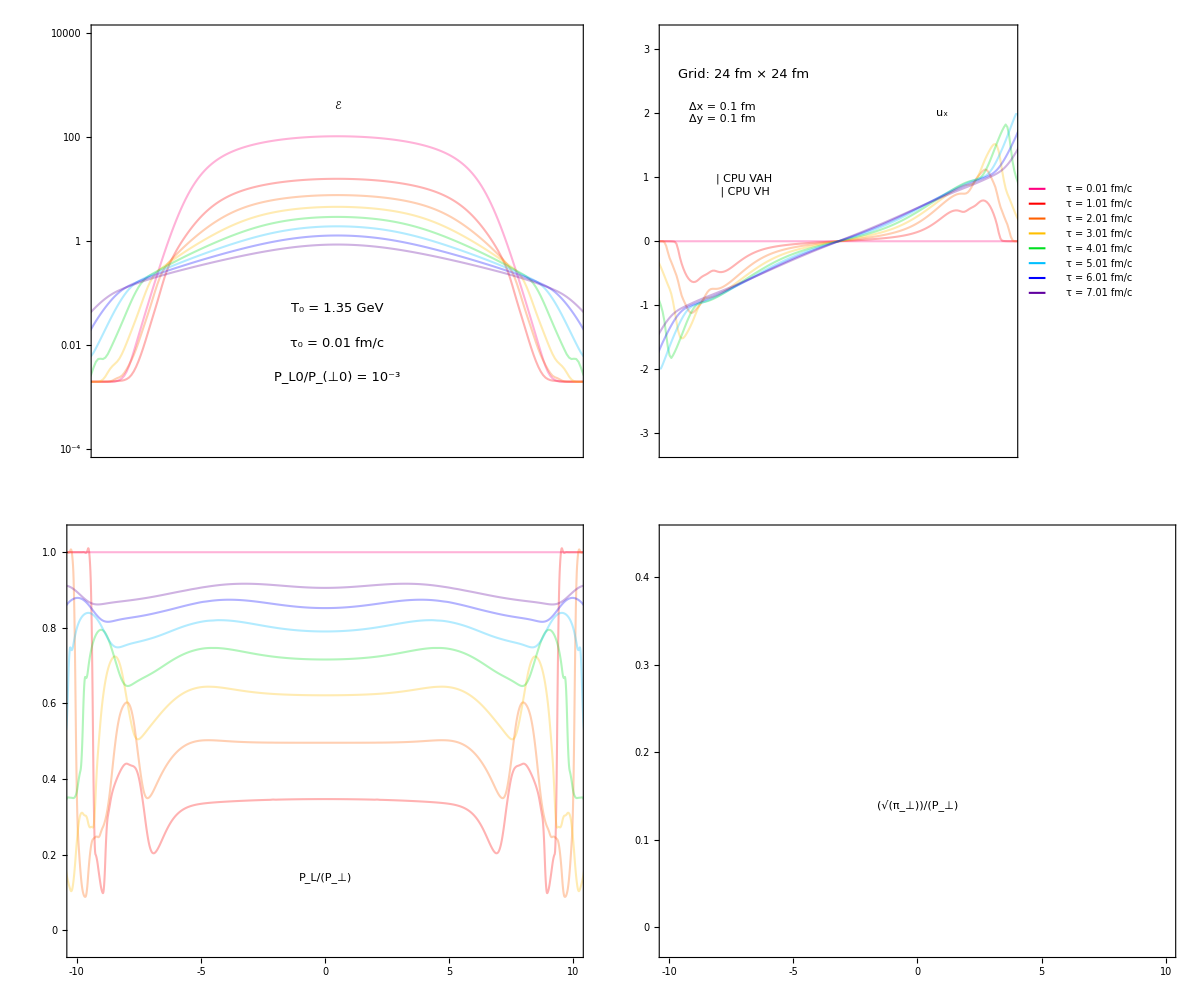
-Graphics-x (fm)

```mathematica
image=400;
aspect=1;
a=30;
b=30;
c=15;
d=10;

Panel[GraphicsGrid[{
{ListLogPlot[{(*e0viscous,e1viscous,e2viscous,e3viscous,e4viscous,e5viscous,e6viscous,e7viscous,*)e0aniso,e1aniso,e2aniso,e3aniso,e4aniso,e5aniso,e6aniso,e7aniso},Joined->True,InterpolationOrder->1,PlotRange->{{-10,10},{10^-4,10^4}},PlotStyle->style,Frame->True,FrameTicks->{{logticks,nologticks},{noxticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->aspect,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[eLabel,{0,6}],Inset[initTime1,{0,-4.5}],Inset[TLabel1,{0,-3}],Inset[plptLabel1,{0,-6}]},ImageSize->image],

ListPlot[{(*ux0viscous,ux1viscous,ux2viscous,ux3viscous,ux4viscous,ux5viscous,ux6viscous,ux7viscous,*)ux0aniso,ux1aniso,ux2aniso,ux3aniso,ux4aniso,ux5aniso,ux6aniso,ux7aniso},Joined->True,InterpolationOrder->1,PlotRange->{{-10,10},{-3.25,3.25}},PlotStyle->style,Frame->True,FrameTicks->{{uxticks, nouxticks},{noxticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->aspect,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[uxLabel,{6,2}],Inset[legend1,{-5.5,0.875}],Inset[gridLabel1,{-5.5,2.6}],Inset[spaceresLabel1,{-6.75,2}],Inset[legendTimes3,{4,-1.75}]},ImageSize->image]},

{ListPlot[{(*plpt0viscous,plpt1viscous,plpt2viscous,plpt3viscous,plpt4viscous,plpt5viscous,plpt6viscous,plpt7viscous,*)plpt0aniso,plpt1aniso,plpt2aniso,plpt3aniso,plpt4aniso,plpt5aniso,plpt6aniso,plpt7aniso},Joined->True,InterpolationOrder->2,PlotRange->{{-10,10},{-0.05,1.05}},PlotStyle->style,Frame->True,FrameTicks->{{oneticks,nooneticks},{xticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->aspect,ImagePadding->{{a,b},{c,d}},Epilog->Inset[plptLabel,{0,0.14}],ImageSize->image],

ListPlot[{(*pi0viscous,pi1viscous,pi2viscous,pi3viscous,pi4viscous,pi5viscous,pi6viscous,pi7viscous,*)pi0aniso,pi1aniso,pi2aniso,pi3aniso,pi4aniso,pi5aniso,pi6aniso,pi7aniso},Joined->True,InterpolationOrder->2,PlotRange->{{-10,10},{-0.025,0.45}},PlotStyle->style,Frame->True,FrameTicks->{{piticks,nopiticks},{xticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->aspect,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[piLabel,{0,0.14}]},ImageSize->image]}
},
ImageSize->{1200,1000},Spacings->{-10,-0*64.5}],
{Style["x (fm)",FontFamily->"Arial",FontSize->16]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->{{-33,-55.5},{-15,-23}},Background->White]

Export[wd<>"/conformal_optical_glauber_central.pdf",%];
```

```mathematica
timeticks = {{0.01,"0.01",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"0.1",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"1.0",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"10",maj},{20,"",min}};

notimeticks = {{0.01,"",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"",maj},{20,"",min}};

dtAdapt =Import[anisoPath<>"/dt_adaptive.dat"];
dtAdapt=Join[{{0.01,0.0005}},dtAdapt];
dtAdapt=Interpolation[dtAdapt];

dtCFL = Import[anisoPath<>"/dt_CFL.dat"];
dtCFL=Interpolation[dtCFL];

delta0=Panel[Grid[{{Style["δ_0 = 0.004",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
alpha=Panel[Grid[{{Style["α = 0.5",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
dt=Panel[Grid[{{Style["Δτ_n",FontSize->18,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
CFL=Panel[Grid[{{Style["Δτ_CFL",FontSize->18,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];

timestep=LogLogPlot[{dtCFL[t],dtAdapt[t]},{t,t0,tf},PlotRange->{{t0,tf},{10^-4,1}},Frame->True,FrameTicks->{{logticks,nologticks},{timeticks,notimeticks}},PlotStyle->{redTran,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->400,Epilog->{Inset[dt,{-3,-4.75}],Inset[CFL,{-2.,-1.5}],Inset[delta0,{1,-2.}],Inset[alpha,{0.91,-3.}]}];

timeplot=Panel[GraphicsGrid[{{timestep}},Spacings->{0,0}],{Style["τ (fm/c)",FontFamily->"Arial",FontSize->16]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White];

Export[wd<>"/optical_glauber_timestep.pdf",%];
```